```mathematica
Lead=ParallelTable[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/51AGNR/lead"<>ToString[x]<>".dat"]],{x,Range[0.01,2.99,0.01]}]
```

{{{-0.00826855-0.0000827321 ⅈ,-0.586356-3.92193×10^-6 ⅈ,0.00240498+0.0000240572 ⅈ,0.25297+3.48788×10^-6 ⅈ,95,0.33341+9.15117×10^-7 ⅈ,0.00413128+0.0000413821 ⅈ,-0.413726+2.26775×10^-6 ⅈ},{1},98,{1},{1}},298}
 |  |  |  |

```mathematica
Clear[β]
```

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[Round[ω*100]]](* Module[{unit=Inverse[β[ω,δ,t,ϵ,51]],J=Inverse[β[ω,δ,t,ϵ,51]]},Do[J= Inverse[IdentityMatrix[102]-unit.T1[t,51].J.T1[t,51]].unit,x];J=J]*)
```

```mathematica
(*leadgenerateleft[ω_,δ_,t_,ϵ_,m_]:= leadgenerateleft[ω,δ,t,ϵ,m]= Module[{unit=Inverse[β[ω,δ,t,ϵ,m]],J=Inverse[β[ω,δ,t,ϵ,m]]},Do[J= Inverse[IdentityMatrix[2m]-unit.T1[t,m].J.T1[t,m]].unit,150000];J=J]*)
```

```mathematica
(*leadgenerateleft[0,0.0001,1,0,51]*)
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-LEFT[ω,δ,t,ϵ].ρ[t,m].LEFT[ω,δ,t,ϵ].ρ[t,m]].LEFT[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

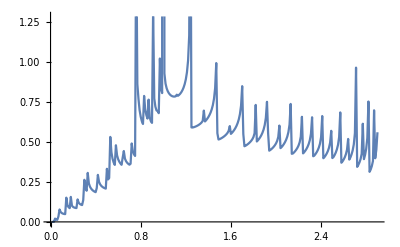

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0,51][[25,25]]]},{ω,Range[0.01,2.9,0.01]}]]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=tr[ω,δ,t,ϵ,m]=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

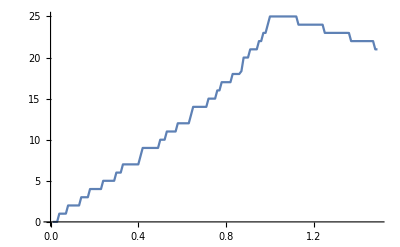

```mathematica
Table[{ω,tr[ω,0.0001,1,0,51]},{ω,Range[0.01,1.49,0.01]}]//ListLinePlot
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,50](*,s[38,50,38,50]*)],concentration],RandomSample[Join[s[1,100,51,102](*,s[38,50,1,37]*)],total-concentration]],First],1000]
```

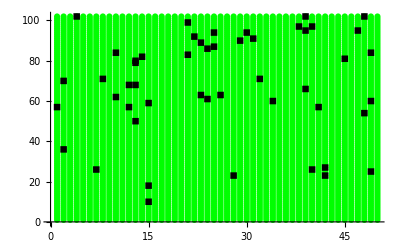

```mathematica
ListPlot[{s[1,50,1,102],dist[50,10][[515]]},PlotStyle->{Green,Black},PlotMarkers->Automatic]
```

```mathematica
dist[50,20][[12]]
```

{{1,88},{7,28},{7,54},{12,33},{13,30},{14,24},{18,20},{20,61},{21,23},{25,4},{28,2},{32,31},{32,66},{34,8},{35,102},{36,33},{37,54},{39,52},{40,67},{42,82},{42,96},{44,31},{45,68},{46,62},{51,72},{52,16},{52,27},{54,97},{55,94},{56,63},{57,76},{59,41},{64,94},{66,43},{66,54},{71,81},{74,56},{75,10},{75,97},{77,69},{78,28},{84,80},{86,53},{89,67},{93,10},{95,61},{96,88},{96,94},{100,31},{100,63}}

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,unitcell_,total_,concentration_,number_]:=Inverse[Module[{J=β[ω,δ,t,ϵ,51],abc=dist[total,concentration][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]]
```

```mathematica
Clear[CA]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_]:=Module[{SSL=SL[ω,0.0001,1,0,51],Tin=T1[1,51],T=ρ[1,51],abc=dist[total,concentration][[number]]},
sl1= Module[{J=SL[ω,0.0001,1,0,51]},
Do[
J=Inverse[IdentityMatrix[102]-f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number].ConjugateTranspose[Tin].J.Tin].f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number],{unitcell,50}];
J=J];
Il1:=Inverse[IdentityMatrix[102]-sl1.T.SSL.T].sl1;
Ir1:=Inverse[IdentityMatrix[102]-SSL.T.sl1.T].SSL;
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:=SSL.T.Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
tra=Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]];
If[tra>tr[ω,0.0001,1,0,51],tr[ω,0.0001,1,0,51],tra]]
```

```mathematica
CA[1,0.0001,1,0,1,15,7,2]
```

2.66646

```mathematica
tra50:=tra50=ParallelTable[{ω,CA[ω,0.0001,1,0,0.5,50,25,12]},{ω,Range[0.5,2.9,0.01]}]
```

```mathematica
tra25:=tra25=ParallelTable[{ω,CA[ω,0.0001,1,0,0.5,25,13,12]},{ω,Range[0.5,2.9,0.01]}]
```

```mathematica
traa50:=traa50=ParallelTable[{ω,CA[ω,0.0001,1,0,0.5,50,25,12]},{ω,Range[0.45,2.9,0.01]}]
```

```mathematica
traa25:=traa25=ParallelTable[{ω,CA[ω,0.0001,1,0,0.5,25,13,12]},{ω,Range[0.45,2.9,0.01]}]
```

```mathematica
Dimensions[traa25]
```

{111,2}

```mathematica
tra1:=Import["~/PhD/quantum_sudoq/tra1.dat"]
```

```mathematica
misfit1:= Import["~/PhD/quantum_sudoq/misfit_50_1.dat"]
```

```mathematica
misfit2:= Import["~/PhD/quantum_sudoq/misfit_50_2.dat"]
```

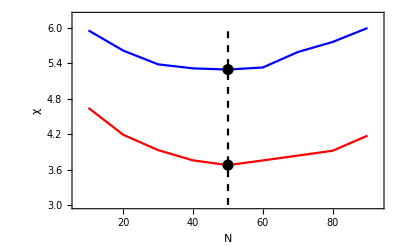

```mathematica
Show[ListLinePlot[{misfit1,misfit2,Table[{50,x},{x,Range[3,6.3]}]},PlotStyle->{Blue,Red,Directive[Black,Dashed]},Frame->True,PlotRange->{{7,93},{3,6.2}},FrameLabel->{{Text[Style[χ,25,FontFamily->"Times New Roman"]],None},{Text[Style["N",30,FontFamily->"Times New Roman"]],None}},LabelStyle->{FontFamily->"Times New Roman",20,GrayLevel[0]}],ListPlot[{misfit1[[5]],misfit2[[5]]},PlotStyle->Directive[Black,PointSize[0.02]]]]
```

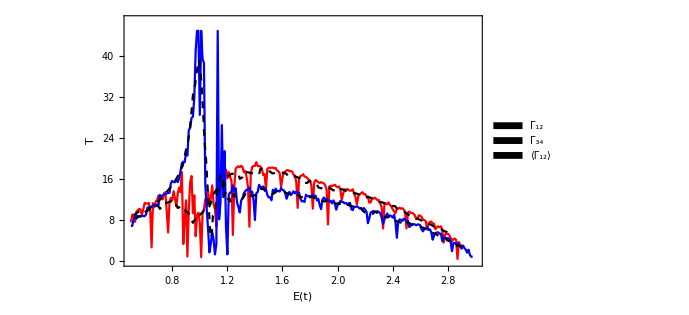

```mathematica
xxx=Show[ListLinePlot[{tra50,tra1,MovingAverage[traa50,15],MovingAverage[tra1,8]},PlotStyle->{Red,Blue,Directive[Dashed,Black],Directive[Dashed,Black]},PlotLegends->Placed[legend,{0.05,0.9}],FrameLabel->{{HoldForm[Τ],None},{HoldForm[Ε[t]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",20,GrayLevel[0.1]},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black],Frame->True,ImageSize->{1100,785},PlotRange->{{0.5,3},{0,47}}]]
```

```mathematica
legend=SwatchLegend[{Red,Blue,Directive[Dashed,Black]},{"Γ_12","Γ_34","⟨Γ_12⟩"},LegendMarkers->Graphics[{(*EdgeForm[Black],*)Rectangle[]}],LegendFunction->(Framed[#(*,RoundingRadius->2*)]&),LegendMargins->10]
```

```mathematica
Show[Show[ListLinePlot[{tra50,MovingAverage[traa50,15]},PlotStyle->{Red,Directive[Dashed,Black]},PlotLegends->Placed[legend,{0.07,0.85}],FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black],Frame->True,ImageSize->{600,470},PlotRange->{{0.5,3},{0,45}}],b],FrameLabel->{{Text[Style[𝒯,30,FontFamily->"Times New Roman"]],None},{Text[Style["E/t",30,FontFamily->"Times New Roman"]],None}},LabelStyle->{FontFamily->"Times New Roman",22,GrayLevel[0]},(*Epilog->{(*Dynamic[If[True,*)Locator[{2.37,32.3},D1,ImageSize->350](*{}]]*)},*)Epilog->{(*Dynamic[If[True,*)Locator[{2.37,32.3},Show[ListLinePlot[{misfit1,misfit2,Table[{50,x},{x,Range[3,6.3]}]},PlotStyle->{Blue,Red,Directive[Black,Dashed]},Frame->True,PlotRange->{{7,93},{3,6.2}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Text[Style[χ,20,FontFamily->"Times New Roman"]],None},{Text[Style["N",20,FontFamily->"Times New Roman"]],None}},LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}],ListPlot[{misfit1[[5]],misfit2[[5]]},PlotStyle->Directive[Black,PointSize[0.02]]]],ImageSize->250](*{}]]*)}]
```

-Graphics-

```mathematica
Export["~/PhD/quantum_sudoq/fig_1_b_new_3.pdf",Show[Show[ListLinePlot[{tra50,MovingAverage[traa50,15]},PlotStyle->{Red,Directive[Dashed,Black]},PlotLegends->Placed[legend,{0.07,0.85}],FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black],Frame->True,ImageSize->900,PlotRange->{{0.5,3},{0,45}}],b],FrameLabel->{{Text[Style[𝒯,50,FontFamily->"Times New Roman"]],None},{Text[Style["E/t",50,FontFamily->"Times New Roman"]],None}},LabelStyle->{FontFamily->"Times New Roman",40,GrayLevel[0]},(*Epilog->{(*Dynamic[If[True,*)Locator[{2.37,32.3},D1,ImageSize->350](*{}]]*)},*)Epilog->{(*Dynamic[If[True,*)Locator[{2.42,32},Show[ListLinePlot[{misfit1,misfit2,Table[{50,x},{x,Range[3,6.3]}]},PlotStyle->{Blue,Red,Directive[Black,Dashed]},Frame->True,PlotRange->{{7,93},{3,6.2}},FrameTicks->{{Range[3,6,1],None},{Range[10,90,20],None}},FrameLabel->{{Text[Style[χ,35,FontFamily->"Times New Roman"]],None},{Text[Style["N",35,FontFamily->"Times New Roman"]],None}},LabelStyle->{FontFamily->"Times New Roman",30,GrayLevel[0]}],ListPlot[{misfit1[[5]],misfit2[[5]]},PlotStyle->Directive[Black,PointSize[0.02]]]],ImageSize->350](*{}]]*)}]]
```

~/PhD/quantum_sudoq/fig_1_b_new_3.pdf

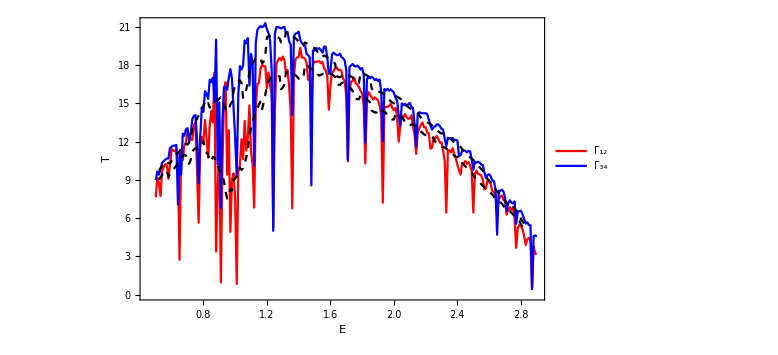

```mathematica
Show[%102,FrameLabel->{{HoldForm[Τ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",25,GrayLevel[0.1]},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black],ImageSize->Large]
```

```mathematica
Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,150,75,n],{n,Range[1,500,1]}]]},{ω,Range[0.01,2.9,0.01]}]
```

$Aborted

```mathematica
Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,100,50,n],{n,Range[1,500,1]}]]},{ω,Range[0.01,2.9,0.01]}]
```

```mathematica
Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,50,25,n],{n,Range[1,500,1]}]]},{ω,Range[0.01,1.2,0.01]}]
```

```mathematica
Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,200,100,n],{n,Range[1,500,1]}]]},{ω,Range[0.01,2.9,0.01]}]
```

```mathematica
Mean[%29]
```

21.3921

```mathematica
MovingAverage[tra50,10]
```

{{0.055,0.97884},{0.065,1.17797},{0.075,1.37626},{0.085,1.5748},{0.095,1.75848},{0.105,1.94996},{0.115,2.1433},{0.125,2.33558},{0.135,2.36854},{0.145,2.52886},{0.155,2.71282},{0.165,2.90247},{0.175,3.09544},{0.185,3.2837},{0.195,3.4538},{0.205,3.65211},{0.215,3.84618},{0.225,4.04629},{0.235,4.30887},{0.245,4.42768},{0.255,4.58976},{0.265,4.7649},{0.275,4.9457},{0.285,5.17586},{0.295,5.38396},{0.305,5.55856},{0.315,5.74718},{0.325,5.93279},{0.335,6.1245},{0.345,6.3295},{0.355,6.46254},{0.365,6.61189},{0.375,6.84453},{0.385,6.97383},{0.395,7.16529},{0.405,7.34203},{0.415,7.51422},{0.425,7.68434},{0.435,7.85158},{0.445,7.98153},{0.455,7.92719},{0.465,8.08915},{0.475,7.99994},{0.485,8.01696},{0.495,8.11039},{0.505,8.22694},{0.515,8.39874},{0.525,8.53388},{0.535,8.60562},{0.545,8.76622},{0.555,9.23762},{0.565,9.49318},{0.575,9.90114},{0.585,10.2797},{0.595,10.3313},{0.605,9.64712},{0.615,9.58433},{0.625,9.65647},{0.635,9.95021},{0.645,10.2284},{0.655,10.4382},{0.665,10.5744},{0.675,10.5122},{0.685,10.6622},{0.695,10.99},{0.705,12.0978},{0.715,11.7691},{0.725,11.0499},{0.735,10.6743},{0.745,10.4795},{0.755,10.5785},{0.765,10.7754},{0.775,10.9994},{0.785,10.5235},{0.795,10.6394},{0.805,10.7095},{0.815,11.4698},{0.825,12.5271},{0.835,13.6883},{0.845,13.2663},{0.855,12.7333},{0.865,11.3639},{0.875,11.0995},{0.885,11.8292},{0.895,12.0645},{0.905,11.5538},{0.915,11.7427},{0.925,11.2656},{0.935,11.0226},{0.945,11.2979},{0.955,12.0336},{0.965,12.9315},{0.975,12.952},{0.985,12.5158},{0.995,12.2124},{1.005,12.8522},{1.015,12.6433},{1.025,13.1026},{1.035,12.7123},{1.045,13.2024},{1.055,12.6863},{1.065,12.7134},{1.075,12.3541},{1.085,12.711},{1.095,13.0007},{1.105,13.0813},{1.115,13.4854},{1.125,13.9124},{1.135,14.3368},{1.145,14.7275},{1.155,15.256},{1.165,15.8569},{1.175,16.7835},{1.185,16.507},{1.195,15.1437},{1.205,15.1232},{1.215,15.1555},{1.225,15.1936},{1.235,15.2587},{1.245,15.3054},{1.255,15.5529},{1.265,15.7731},{1.275,15.904},{1.285,16.4752},{1.295,17.8233},{1.305,17.6142},{1.315,16.009},{1.325,16.0306},{1.335,16.0819},{1.345,16.188},{1.355,16.2404},{1.365,16.3357},{1.375,16.4551},{1.385,16.5526},{1.395,16.7658},{1.405,17.1516},{1.415,18.6359},{1.425,18.4782},{1.435,17.9915},{1.445,17.8538},{1.455,17.7613},{1.465,17.6539},{1.475,17.6327},{1.485,17.5951},{1.495,17.5604},{1.505,17.5606},{1.515,17.6532},{1.525,17.7074},{1.535,18.0037},{1.545,17.6483},{1.555,17.46},{1.565,17.3708},{1.575,17.2837},{1.585,17.24},{1.595,17.2054},{1.605,17.1478},{1.615,17.0845},{1.625,17.0172},{1.635,17.0038},{1.645,17.1603},{1.655,17.0451},{1.665,16.3497},{1.675,16.2016},{1.685,16.0913},{1.695,15.9854},{1.705,15.9274},{1.715,15.8691},{1.725,15.827},{1.735,15.7491},{1.745,15.7414},{1.755,15.7943},{1.765,16.2675},{1.775,15.4083},{1.785,15.245},{1.795,15.1243},{1.805,14.9752},{1.815,14.8656},{1.825,14.7464},{1.835,14.6666},{1.845,14.6024},{1.855,14.5492},{1.865,14.5162},{1.875,15.1799},{1.885,14.3971},{1.895,14.3057},{1.905,14.2262},{1.915,14.1952},{1.925,14.1447},{1.935,14.0879},{1.945,14.0425},{1.955,14.0058},{1.965,13.9859},{1.975,13.9746},{1.985,14.4527},{1.995,14.3091},{2.005,14.2389},{2.015,14.1132},{2.025,14.0499},{2.035,13.9522},{2.045,13.842},{2.055,13.7369},{2.065,13.6284},{2.075,13.5383},{2.085,13.4916},{2.095,13.0302},{2.105,12.9331},{2.115,12.8606},{2.125,12.737},{2.135,12.6419},{2.145,12.5652},{2.155,12.481},{2.165,12.3987},{2.175,12.3101},{2.185,12.2346},{2.195,12.3961},{2.205,12.3011},{2.215,12.2083},{2.225,12.16},{2.235,12.0834},{2.245,11.9711},{2.255,11.8698},{2.265,11.7723},{2.275,11.6363},{2.285,11.534},{2.295,11.6413},{2.305,11.5778},{2.315,11.4897},{2.325,11.3842},{2.335,11.2857},{2.345,11.1946},{2.355,11.1186},{2.365,10.9992},{2.375,10.9157},{2.385,10.9935},{2.395,10.915},{2.405,10.791},{2.415,10.6875},{2.425,10.5902},{2.435,10.4875},{2.445,10.3362},{2.455,9.82866},{2.465,9.69198},{2.475,9.64335},{2.485,9.5249},{2.495,9.40205},{2.505,9.29058},{2.515,9.15756},{2.525,8.94128},{2.535,8.75579},{2.545,8.70882},{2.555,8.98587},{2.565,8.90212},{2.575,8.83325},{2.585,8.68764},{2.595,8.49549},{2.605,8.24368},{2.615,8.13564},{2.625,8.09096},{2.635,8.03496},{2.645,7.86607},{2.655,7.70772},{2.665,7.44725},{2.675,7.21699},{2.685,7.09292},{2.695,7.02721},{2.705,7.01363},{2.715,6.85839},{2.725,6.46505},{2.735,6.25655},{2.745,6.08659},{2.755,5.90987},{2.765,5.85169},{2.775,5.70783},{2.785,5.47189},{2.795,5.27943},{2.805,5.09626},{2.815,4.86608},{2.825,5.0448},{2.835,4.86834},{2.845,4.69619},{2.855,4.5209},{2.865,4.13761},{2.875,3.9339},{2.885,3.76847},{2.895,3.4793},{2.905,3.18615},{2.915,2.93565},{2.925,2.40366},{2.935,2.08003},{2.945,1.78986}}

```mathematica
Dimensions[Range[1.11,2.81,0.01]]
```

{171}

```mathematica
Table[CA[ω,0.0001,1,0,1,15,7,2],{ω,Range[1.11,2.95,0.01]}]
```

{10.1423,4.56945,11.4253,13.0212,12.9007,13.9185,14.7983,13.0475,15.0474,13.5605,14.5673,14.0342,12.8117,2.79752,13.472,14.1945,14.4155,14.8681,15.4218,14.7232,14.9318,15.1611,14.3603,14.2454,12.9726,2.6987,14.0869,14.8927,14.9688,15.7786,15.3727,15.3071,15.7626,14.909,14.8074,13.9922,12.1837,8.9245,14.0394,14.6914,14.8868,14.838,15.0938,15.4441,14.6164,14.5737,14.3293,14.0517,12.2795,14.1497,14.2837,14.0866,14.0552,14.1417,14.5037,14.5993,14.4933,13.9751,13.5482,12.0424,6.03386,12.917,13.5887,13.7636,14.1059,13.5565,13.824,13.5853,13.518,13.1967,11.6298,6.67437,12.4759,12.6411,13.0936,13.279,13.1663,13.0186,12.8276,12.9554,11.9235,11.714,10.948,11.3628,11.9448,12.0509,12.4327,12.0343,12.2558,11.7866,11.9752,11.2863,8.90174,9.73477,10.913,11.3796,11.357,11.1611,11.329,11.3825,11.4417,10.4796,10.0053,9.79606,10.2665,10.698,10.4831,10.9119,10.4612,10.651,10.6448,10.2265,8.24676,9.33251,9.49722,9.60525,9.52677,9.3918,9.82846,9.47989,8.76764,7.50438,6.89404,8.69086,8.86638,8.87543,8.9404,9.25165,8.87659,8.33839,6.46613,7.05455,7.7547,8.05784,8.01294,8.22135,8.2646,7.36851,6.36491,4.9669,6.72245,7.12485,7.09631,7.14453,6.54803,6.48251,5.13298,5.21415,5.62438,5.90463,5.82521,5.54792,5.80186,5.17501,4.68109,4.90853,5.00229,4.76281,5.16512,4.60638,2.83359,3.65314,4.23193,4.59977,4.05817,3.85466,2.43282,3.52062,3.5486,3.05427,3.44919,2.59353,2.69786,2.81009,2.6267,2.27247,2.29743,1.96925,1.66616,1.63598,0.340814,1.2143,0.859273,0.246829,0.405787}

```mathematica
MovingAverage[%139,3]
```

{8.71233,9.67196,12.449,13.2801,13.8725,13.9214,14.2977,13.8852,14.3918,14.054,13.8044,9.88116,9.69375,10.1547,14.0273,14.4927,14.9018,15.0044,15.0256,14.9387,14.8177,14.5889,13.8594,9.97221,9.91938,10.5594,14.6495,15.2134,15.3734,15.4861,15.4808,15.3262,15.1597,14.5695,13.6611,11.7001,11.7159,12.5518,14.5392,14.8054,14.9395,15.1253,15.0514,14.878,14.5064,14.3182,13.5535,13.4936,13.571,14.1733,14.1418,14.0945,14.2335,14.4149,14.5321,14.3559,14.0055,13.1885,10.5415,10.3311,10.8465,13.4231,13.8194,13.8087,13.8288,13.6553,13.6425,13.4333,12.7815,10.5003,10.26,10.5971,12.7369,13.0046,13.1796,13.1546,13.0042,12.9339,12.5689,12.1977,11.5285,11.3416,11.4186,11.7862,12.1428,12.1727,12.2409,12.0256,12.0059,11.6827,10.7211,9.97426,9.84984,10.6758,11.2165,11.2992,11.2824,11.2909,11.3844,11.1013,10.6422,10.0937,10.0226,10.2535,10.4825,10.6977,10.6187,10.6747,10.5856,10.5074,9.70601,9.26859,9.02549,9.47833,9.54308,9.50794,9.58234,9.56672,9.35866,8.58397,7.72202,7.69643,8.15043,8.81089,8.89407,9.02249,9.02288,8.82221,7.8937,7.28636,7.09179,7.62236,7.94183,8.09738,8.1663,7.95149,7.33267,6.23344,6.01809,6.2714,6.9812,7.1219,6.92963,6.72502,6.0545,5.60988,5.32384,5.58106,5.78474,5.75925,5.725,5.50826,5.21932,4.92154,4.86397,4.89121,4.97674,4.84477,4.2017,3.6977,3.57288,4.16161,4.29662,4.17087,3.44855,3.26937,3.16735,3.3745,3.35069,3.03233,2.91353,2.70049,2.71155,2.56975,2.39887,2.17972,1.97761,1.75713,1.21432,1.0637,0.804796,0.773467,0.503963}

```mathematica
Length[%157]
```

183

```mathematica
Dimensions[Range[1.11,2.93,0.01]]
```

{183}

```mathematica
Transpose[Join[{Range[1.11,2.93,0.01]},{%157}]]
```

{{1.11,8.71233},{1.12,9.67196},{1.13,12.449},{1.14,13.2801},{1.15,13.8725},{1.16,13.9214},{1.17,14.2977},{1.18,13.8852},{1.19,14.3918},{1.2,14.054},{1.21,13.8044},{1.22,9.88116},{1.23,9.69375},{1.24,10.1547},{1.25,14.0273},{1.26,14.4927},{1.27,14.9018},{1.28,15.0044},{1.29,15.0256},{1.3,14.9387},{1.31,14.8177},{1.32,14.5889},{1.33,13.8594},{1.34,9.97221},{1.35,9.91938},{1.36,10.5594},{1.37,14.6495},{1.38,15.2134},{1.39,15.3734},{1.4,15.4861},{1.41,15.4808},{1.42,15.3262},{1.43,15.1597},{1.44,14.5695},{1.45,13.6611},{1.46,11.7001},{1.47,11.7159},{1.48,12.5518},{1.49,14.5392},{1.5,14.8054},{1.51,14.9395},{1.52,15.1253},{1.53,15.0514},{1.54,14.878},{1.55,14.5064},{1.56,14.3182},{1.57,13.5535},{1.58,13.4936},{1.59,13.571},{1.6,14.1733},{1.61,14.1418},{1.62,14.0945},{1.63,14.2335},{1.64,14.4149},{1.65,14.5321},{1.66,14.3559},{1.67,14.0055},{1.68,13.1885},{1.69,10.5415},{1.7,10.3311},{1.71,10.8465},{1.72,13.4231},{1.73,13.8194},{1.74,13.8087},{1.75,13.8288},{1.76,13.6553},{1.77,13.6425},{1.78,13.4333},{1.79,12.7815},{1.8,10.5003},{1.81,10.26},{1.82,10.5971},{1.83,12.7369},{1.84,13.0046},{1.85,13.1796},{1.86,13.1546},{1.87,13.0042},{1.88,12.9339},{1.89,12.5689},{1.9,12.1977},{1.91,11.5285},{1.92,11.3416},{1.93,11.4186},{1.94,11.7862},{1.95,12.1428},{1.96,12.1727},{1.97,12.2409},{1.98,12.0256},{1.99,12.0059},{2.,11.6827},{2.01,10.7211},{2.02,9.97426},{2.03,9.84984},{2.04,10.6758},{2.05,11.2165},{2.06,11.2992},{2.07,11.2824},{2.08,11.2909},{2.09,11.3844},{2.1,11.1013},{2.11,10.6422},{2.12,10.0937},{2.13,10.0226},{2.14,10.2535},{2.15,10.4825},{2.16,10.6977},{2.17,10.6187},{2.18,10.6747},{2.19,10.5856},{2.2,10.5074},{2.21,9.70601},{2.22,9.26859},{2.23,9.02549},{2.24,9.47833},{2.25,9.54308},{2.26,9.50794},{2.27,9.58234},{2.28,9.56672},{2.29,9.35866},{2.3,8.58397},{2.31,7.72202},{2.32,7.69643},{2.33,8.15043},{2.34,8.81089},{2.35,8.89407},{2.36,9.02249},{2.37,9.02288},{2.38,8.82221},{2.39,7.8937},{2.4,7.28636},{2.41,7.09179},{2.42,7.62236},{2.43,7.94183},{2.44,8.09738},{2.45,8.1663},{2.46,7.95149},{2.47,7.33267},{2.48,6.23344},{2.49,6.01809},{2.5,6.2714},{2.51,6.9812},{2.52,7.1219},{2.53,6.92963},{2.54,6.72502},{2.55,6.0545},{2.56,5.60988},{2.57,5.32384},{2.58,5.58106},{2.59,5.78474},{2.6,5.75925},{2.61,5.725},{2.62,5.50826},{2.63,5.21932},{2.64,4.92154},{2.65,4.86397},{2.66,4.89121},{2.67,4.97674},{2.68,4.84477},{2.69,4.2017},{2.7,3.6977},{2.71,3.57288},{2.72,4.16161},{2.73,4.29662},{2.74,4.17087},{2.75,3.44855},{2.76,3.26937},{2.77,3.16735},{2.78,3.3745},{2.79,3.35069},{2.8,3.03233},{2.81,2.91353},{2.82,2.70049},{2.83,2.71155},{2.84,2.56975},{2.85,2.39887},{2.86,2.17972},{2.87,1.97761},{2.88,1.75713},{2.89,1.21432},{2.9,1.0637},{2.91,0.804796},{2.92,0.773467},{2.93,0.503963}}

```mathematica
Dimensions[%]
```

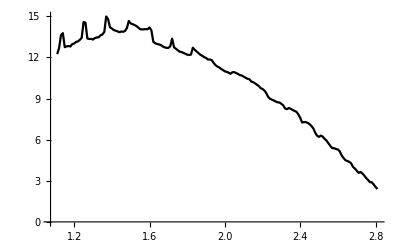

```mathematica
ListPlot[%126,Joined->True,PlotStyle->Black]
```

```mathematica
Length[%89]
```

171

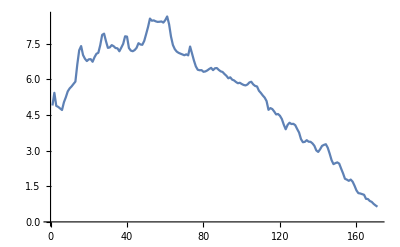

```mathematica
ListPlot[%89,Joined->True]
```

```mathematica
Show[ListLinePlot[ParallelTable[{ω,CA[ω,0.0001,1,0,1,15,7,2]},{ω,Range[1.11,2.99,0.01]}],PlotStyle->Blue,Frame->True,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}],ListLinePlot[%160,PlotStyle->{Dashed,Black},ImageSize->{500,500}],PlotRange->{{1.1,2.81},{0,25.5}}]
```

```mathematica
Show[ListLinePlot[ParallelTable[{ω,CA[ω,0.0001,1,0,1,50,25,2]},{ω,Range[1.11,2.99,0.01]}],PlotStyle->Red,Frame->True,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}],ListLinePlot[%3,PlotStyle->Black],PlotRange->{{1.1,2.81},{0,25.5}}]
```

```mathematica
Show[Graphics[{Rectangle[{0,0},{1,1},a],Rectangle[{0.56,0.37},{1,1},b]}],ImageSize->{700,500}]
```

```mathematica
Graphics[First[a],Inset[b,{2.5,10},Automatic,Scaled[0.5],AbsoluteOptions[a]]]
```

Ticks::ticks: {Automatic,Automatic} is not a valid tick specification.

General::stop: Further output of Ticks::ticks will be suppressed during this calculation.

```mathematica
Export["/home/shardulmukim/PhD/quantum_sudoq/fig_1_b.pdf",%38,"PDF"]
```

/home/shardulmukim/PhD/quantum_sudoq/fig_1_b.pdf

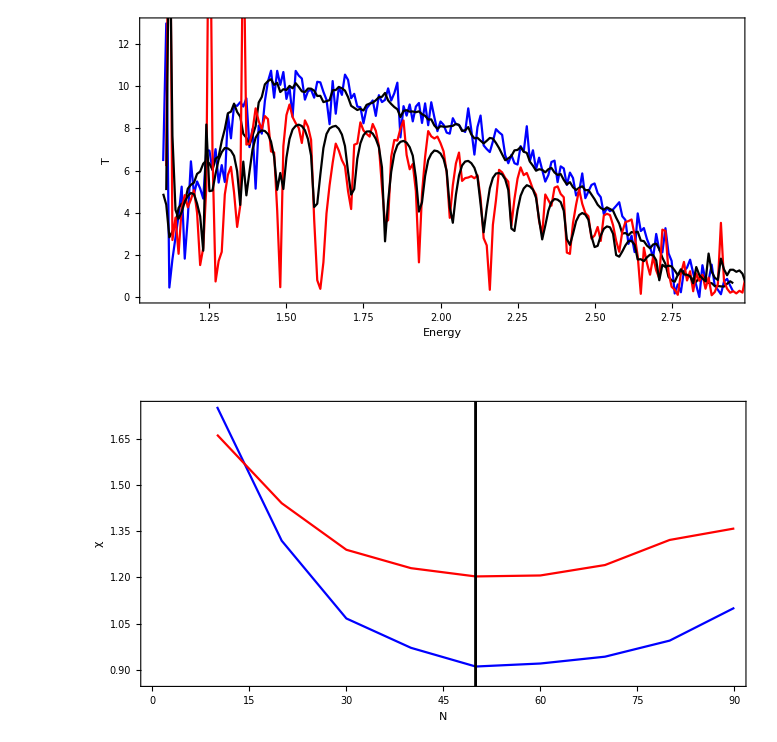

```mathematica
Show[]
```

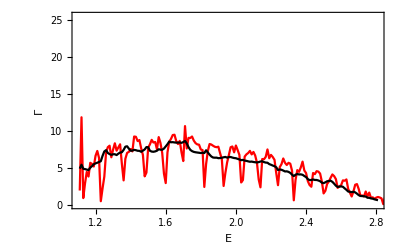

-Graphics-

```mathematica
Τ
```

```mathematica
Show[%165,%167]
```

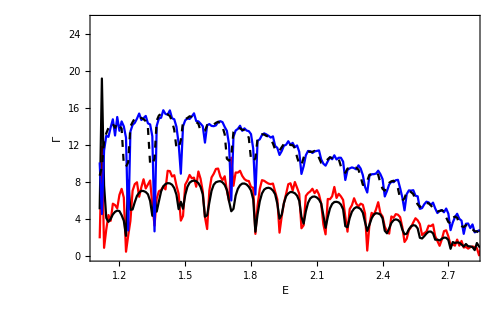

-Graphics-

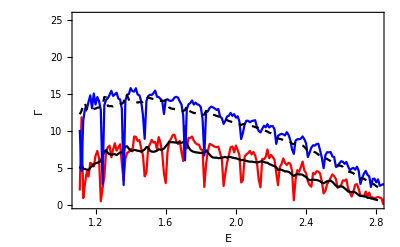

-Graphics-

```mathematica
Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,50,25,n],{n,500}]]},{ω,Range[1.11,2.99,0.01]}]
```

```mathematica
{{1.11,5.0836382657701575},{1.12,19.20357240707884},{1.1300000000000001,7.658441534728387},{1.1400000000000001,4.142846181712659},{1.1500000000000001,3.7286150935488567},{1.1600000000000001,4.042407275599511},{1.1700000000000002,4.5316611671427705},{1.1800000000000002,4.807335863692477},{1.1900000000000002,4.944390873167992},{1.2000000000000002,4.889448317279504},{1.2100000000000002,4.443100193101643},{1.2200000000000002,3.843383009097895},{1.23,2.215102096104861},{1.2400000000000002,8.187736312557044},{1.25,5.031732211926874},{1.26,5.065148725904594},{1.27,5.856610914096784},{1.28,6.533350709235164},{1.29,6.878718934404381},{1.3,7.077626594918484},{1.31,7.054297516250087},{1.32,6.947887750620152},{1.33,6.703309295035277},{1.34,5.982060404164915},{1.35,4.380663382452187},{1.36,6.432757394716863},{1.37,4.834573774891086},{1.3800000000000001,5.946195821519792},{1.3900000000000001,7.010573380926424},{1.4000000000000001,7.5612625259330235},{1.4100000000000001,7.813630173536941},{1.4200000000000002,7.908049559861914},{1.4300000000000002,7.879808384106717},{1.4400000000000002,7.734079177296811},{1.4500000000000002,7.376144658159515},{1.4600000000000002,6.659640159547082},{1.4700000000000002,5.0975313974252145},{1.48,5.892729694448064},{1.4900000000000002,5.135887487945232},{1.5,6.617420801880781},{1.5100000000000002,7.504651473756153},{1.52,7.9538149436121754},{1.53,8.124771504632239},{1.54,8.180986354888908},{1.55,8.114721214071453},{1.56,7.915346562976316},{1.57,7.493327352464524},{1.58,6.712657824532524},{1.59,4.281883869572263},{1.6,4.439870433393081},{1.61,5.814990333250182},{1.62,7.0758126501968075},{1.6300000000000001,7.7370007873870446},{1.6400000000000001,8.003874002941934},{1.6500000000000001,8.086572445179897},{1.6600000000000001,8.12402430045676},{1.6700000000000002,7.987139652332535},{1.6800000000000002,7.713902602464963},{1.69,7.165683339389505},{1.7000000000000002,5.9484060649516115},{1.71,4.871007133502977},{1.7200000000000002,5.133331393621937},{1.73,6.56888485383827},{1.7400000000000002,7.297386422340358},{1.75,7.680693259023958},{1.7600000000000002,7.856438286416092},{1.77,7.864558088824937},{1.7800000000000002,7.75894666276017},{1.79,7.509878065754059},{1.8000000000000003,7.116277651978791},{1.81,6.160780122202867},{1.82,2.657161609758164},{1.83,4.557440634135361},{1.84,5.948355900463281},{1.85,6.796824469877827},{1.86,7.210686437593844},{1.87,7.369191144309783},{1.8800000000000001,7.4112480499040085},{1.8900000000000001,7.328267579878865},{1.9000000000000001,7.114131193928176},{1.9100000000000001,6.712427490535541},{1.9200000000000002,5.682258952131231},{1.9300000000000002,4.066851665749793},{1.9400000000000002,4.5080839111741},{1.9500000000000002,5.7490709180237385},{1.96,6.499300018371248},{1.9700000000000002,6.79890089035496},{1.98,6.956426200110418},{1.9900000000000002,6.925230021275176},{2.,6.813629292849256},{2.0100000000000002,6.553971421175537},{2.02,5.988491836344443},{2.0300000000000002,4.273217764625851},{2.04,3.5366207953499464},{2.0500000000000003,4.862610440496153},{2.06,5.776611487764093},{2.0700000000000003,6.2510558798700275},{2.08,6.435837729977688},{2.09,6.465921775227991},{2.1,6.357885070268655},{2.1100000000000003,6.138300288231428},{2.12,5.703582247810139},{2.13,4.432242269167618},{2.14,3.0876583444711403},{2.1500000000000004,4.233159603637581},{2.16,5.17096276467632},{2.17,5.663140857474067},{2.18,5.869738602502739},{2.1900000000000004,5.890969393602039},{2.2,5.824613615866008},{2.21,5.592589297047304},{2.22,5.083635190871555},{2.2300000000000004,3.2622265906426002},{2.24,3.1498336080046627},{2.25,4.137256386357045},{2.2600000000000002,4.81691673168072},{2.27,5.159936808934072},{2.2800000000000002,5.314594303632026},{2.29,5.25652514707238},{2.3,5.107664569994428},{2.31,4.718111799107184},{2.3200000000000003,3.6852363590980457},{2.33,2.7502009111823247},{2.34,3.40478490482061},{2.35,4.10622047162745},{2.3600000000000003,4.519142041042236},{2.37,4.662337642546827},{2.38,4.63147301421515},{2.39,4.515028253341293},{2.4000000000000004,4.104963022420059},{2.41,2.763979178206866},{2.42,2.4887233392575},{2.43,3.015768917267383},{2.4400000000000004,3.6105111571111093},{2.45,3.9023297127816723},{2.46,3.9988993691198194},{2.47,3.922308845622342},{2.4800000000000004,3.6827705948102603},{2.49,2.892294562581937},{2.5,2.387224699700924},{2.5100000000000002,2.445229157956108},{2.52,2.927963566222177},{2.5300000000000002,3.2528707973686988},{2.54,3.3636381308858},{2.55,3.323653047316214},{2.56,3.0178818790556616},{2.5700000000000003,2.007655508598241},{2.58,1.9313952471743034},{2.59,2.179476880156794},{2.6,2.462770541237976},{2.6100000000000003,2.6704910761815768},{2.62,2.677277227421497},{2.63,2.4959182298823763},{2.64,1.7996044663349835},{2.6500000000000004,1.8129215671740861},{2.66,1.7193002414844045},{2.67,1.9001063659950315},{2.68,2.02835762586551},{2.6900000000000004,2.008879336493949},{2.7,1.7606629282841733},{2.71,0.8162209088057429},{2.72,1.5469542539367518},{2.7300000000000004,1.4416611037154876},{2.74,1.5083556066664485},{2.75,1.470797326634875},{2.7600000000000002,1.280488838347885},{2.7700000000000005,1.058596347742615},{2.7800000000000002,1.3356717136474905},{2.79,1.093388887628537},{2.8,1.0772100609646962},{2.81,1.0072410888852856},{2.8200000000000003,0.6743524949332372},{2.83,1.4423694424396043},{2.84,1.0591290984772945},{2.85,0.9036196886083238},{2.8600000000000003,0.759411785520069},{2.87,2.0802972853733452},{2.88,1.2271354056996973},{2.89,0.9349804857756235},{2.9000000000000004,0.8301362205825634},{2.91,1.8402873903806465},{2.92,1.3311763456676657},{2.93,1.051555552030294},{2.9400000000000004,1.3117961378211325},{2.95,1.313725556203742},{2.96,1.2162657242002946},{2.97,1.2809498823454994},{2.9800000000000004,1.1241125657495992},{2.99,0.6973891898740707}}
```

{{1.11,5.08364},{1.12,19.2036},{1.13,7.65844},{1.14,4.14285},{1.15,3.72862},{1.16,4.04241},{1.17,4.53166},{1.18,4.80734},{1.19,4.94439},{1.2,4.88945},{1.21,4.4431},{1.22,3.84338},{1.23,2.2151},{1.24,8.18774},{1.25,5.03173},{1.26,5.06515},{1.27,5.85661},{1.28,6.53335},{1.29,6.87872},{1.3,7.07763},{1.31,7.0543},{1.32,6.94789},{1.33,6.70331},{1.34,5.98206},{1.35,4.38066},{1.36,6.43276},{1.37,4.83457},{1.38,5.9462},{1.39,7.01057},{1.4,7.56126},{1.41,7.81363},{1.42,7.90805},{1.43,7.87981},{1.44,7.73408},{1.45,7.37614},{1.46,6.65964},{1.47,5.09753},{1.48,5.89273},{1.49,5.13589},{1.5,6.61742},{1.51,7.50465},{1.52,7.95381},{1.53,8.12477},{1.54,8.18099},{1.55,8.11472},{1.56,7.91535},{1.57,7.49333},{1.58,6.71266},{1.59,4.28188},{1.6,4.43987},{1.61,5.81499},{1.62,7.07581},{1.63,7.737},{1.64,8.00387},{1.65,8.08657},{1.66,8.12402},{1.67,7.98714},{1.68,7.7139},{1.69,7.16568},{1.7,5.94841},{1.71,4.87101},{1.72,5.13333},{1.73,6.56888},{1.74,7.29739},{1.75,7.68069},{1.76,7.85644},{1.77,7.86456},{1.78,7.75895},{1.79,7.50988},{1.8,7.11628},{1.81,6.16078},{1.82,2.65716},{1.83,4.55744},{1.84,5.94836},{1.85,6.79682},{1.86,7.21069},{1.87,7.36919},{1.88,7.41125},{1.89,7.32827},{1.9,7.11413},{1.91,6.71243},{1.92,5.68226},{1.93,4.06685},{1.94,4.50808},{1.95,5.74907},{1.96,6.4993},{1.97,6.7989},{1.98,6.95643},{1.99,6.92523},{2.,6.81363},{2.01,6.55397},{2.02,5.98849},{2.03,4.27322},{2.04,3.53662},{2.05,4.86261},{2.06,5.77661},{2.07,6.25106},{2.08,6.43584},{2.09,6.46592},{2.1,6.35789},{2.11,6.1383},{2.12,5.70358},{2.13,4.43224},{2.14,3.08766},{2.15,4.23316},{2.16,5.17096},{2.17,5.66314},{2.18,5.86974},{2.19,5.89097},{2.2,5.82461},{2.21,5.59259},{2.22,5.08364},{2.23,3.26223},{2.24,3.14983},{2.25,4.13726},{2.26,4.81692},{2.27,5.15994},{2.28,5.31459},{2.29,5.25653},{2.3,5.10766},{2.31,4.71811},{2.32,3.68524},{2.33,2.7502},{2.34,3.40478},{2.35,4.10622},{2.36,4.51914},{2.37,4.66234},{2.38,4.63147},{2.39,4.51503},{2.4,4.10496},{2.41,2.76398},{2.42,2.48872},{2.43,3.01577},{2.44,3.61051},{2.45,3.90233},{2.46,3.9989},{2.47,3.92231},{2.48,3.68277},{2.49,2.89229},{2.5,2.38722},{2.51,2.44523},{2.52,2.92796},{2.53,3.25287},{2.54,3.36364},{2.55,3.32365},{2.56,3.01788},{2.57,2.00766},{2.58,1.9314},{2.59,2.17948},{2.6,2.46277},{2.61,2.67049},{2.62,2.67728},{2.63,2.49592},{2.64,1.7996},{2.65,1.81292},{2.66,1.7193},{2.67,1.90011},{2.68,2.02836},{2.69,2.00888},{2.7,1.76066},{2.71,0.816221},{2.72,1.54695},{2.73,1.44166},{2.74,1.50836},{2.75,1.4708},{2.76,1.28049},{2.77,1.0586},{2.78,1.33567},{2.79,1.09339},{2.8,1.07721},{2.81,1.00724},{2.82,0.674352},{2.83,1.44237},{2.84,1.05913},{2.85,0.90362},{2.86,0.759412},{2.87,2.0803},{2.88,1.22714},{2.89,0.93498},{2.9,0.830136},{2.91,1.84029},{2.92,1.33118},{2.93,1.05156},{2.94,1.3118},{2.95,1.31373},{2.96,1.21627},{2.97,1.28095},{2.98,1.12411},{2.99,0.697389}}

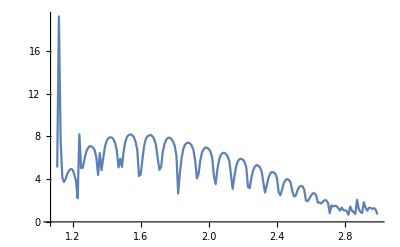

SystemDialogInput::nprmtv: SystemDialogInput is not currently supported within preemptive evaluations.

```mathematica
ListPlot[%134,Joined->True]
```

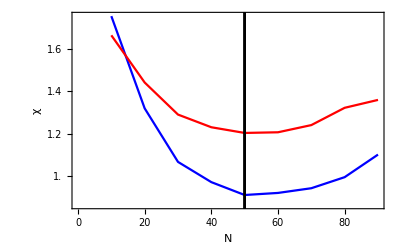
```mathematica
b=-Graphics-
```

-Graphics-

```mathematica
a=Manipulate[Show[ListLinePlot[Table[Import["/home/shardulmukim/PhD/fwi/zgnr/transmission_zgnr_imp.dat"][[x]],{x,Range[111,296]}],Frame->True,PlotRange->{{1.05,3},{0,25}},Epilog->{Dynamic[If[True,Locator[Dynamic[pt],b,ImageSize->250],{}]]},PlotStyle->Blue,Frame->True,FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]},FrameTicks->{{Range[5,20,5],None},{Automatic,None}}],%26,ListLinePlot[Table[Import["/home/shardulmukim/PhD/fwi/zgnr/transmission_zgnr_imp_ca.dat"][[x]],{x,Range[111,296]}],Frame->True,PlotStyle->{Black},PlotRange->{{0,3},{0,25}}],FrameLabel->{{HoldForm[Τ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]},ImageSize->500],{pt,Scaled[{0.5,0.5}],None}]
```

-Graphics-

```mathematica
Export["~/PhD/quantum_sudoq/fig_1b_inset.pdf",%205]
```

~/PhD/quantum_sudoq/fig_1b_inset.pdf

```mathematica
Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,25,25,n],{n,500}]]},{ω,Range[1.11,2.99,0.01]}]
```

{{1.11,3.17675},{1.12,12.7303},{1.13,8.21046},{1.14,7.96985},{1.15,8.97921},{1.16,9.8516},{1.17,10.3596},{1.18,10.4837},{1.19,10.6314},{1.2,10.5642},{1.21,10.2002},{1.22,9.54042},{1.23,8.09499},{1.24,4.25349},{1.25,8.51971},{1.26,10.0617},{1.27,11.1697},{1.28,11.675},{1.29,11.9587},{1.3,12.0671},{1.31,12.002},{1.32,11.8851},{1.33,11.5857},{1.34,10.9785},{1.35,9.75792},{1.36,4.53189},{1.37,8.97715},{1.38,11.0127},{1.39,11.8989},{1.4,12.2725},{1.41,12.4141},{1.42,12.4569},{1.43,12.3844},{1.44,12.2585},{1.45,11.8805},{1.46,11.3016},{1.47,9.91803},{1.48,7.40153},{1.49,9.5492},{1.5,11.2775},{1.51,11.9918},{1.52,12.2239},{1.53,12.3372},{1.54,12.3282},{1.55,12.2304},{1.56,12.0524},{1.57,11.7439},{1.58,11.0039},{1.59,8.88079},{1.6,7.33555},{1.61,10.2814},{1.62,11.4025},{1.63,11.7877},{1.64,11.9738},{1.65,12.0304},{1.66,11.9707},{1.67,11.8072},{1.68,11.5815},{1.69,11.0746},{1.7,10.0102},{1.71,5.49377},{1.72,9.16169},{1.73,10.6715},{1.74,11.2069},{1.75,11.4527},{1.76,11.5079},{1.77,11.4662},{1.78,11.3774},{1.79,11.1917},{1.8,10.7446},{1.81,9.91109},{1.82,4.73723},{1.83,7.97537},{1.84,9.98926},{1.85,10.5832},{1.86,10.8149},{1.87,10.8759},{1.88,10.8755},{1.89,10.732},{1.9,10.5507},{1.91,10.1882},{1.92,9.27111},{1.93,4.92203},{1.94,8.06714},{1.95,9.44583},{1.96,9.94324},{1.97,10.1939},{1.98,10.2048},{1.99,10.1648},{2.,9.98918},{2.01,9.77817},{2.02,9.30657},{2.03,7.66132},{2.04,5.94429},{2.05,8.28547},{2.06,9.06917},{2.07,9.42311},{2.08,9.48455},{2.09,9.42743},{2.1,9.36947},{2.11,9.19516},{2.12,8.74841},{2.13,7.51603},{2.14,5.20971},{2.15,7.4235},{2.16,8.28611},{2.17,8.61828},{2.18,8.6917},{2.19,8.67908},{2.2,8.57108},{2.21,8.3188},{2.22,7.84701},{2.23,6.07848},{2.24,5.24977},{2.25,6.91241},{2.26,7.56858},{2.27,7.8211},{2.28,7.85314},{2.29,7.79813},{2.3,7.63357},{2.31,7.2983},{2.32,6.29498},{2.33,4.13158},{2.34,6.00015},{2.35,6.70691},{2.36,7.00912},{2.37,7.06452},{2.38,7.0408},{2.39,6.88502},{2.4,6.52594},{2.41,5.28551},{2.42,4.17836},{2.43,5.46438},{2.44,6.05988},{2.45,6.25523},{2.46,6.28028},{2.47,6.1732},{2.48,5.91896},{2.49,5.13479},{2.5,3.23016},{2.51,4.46118},{2.52,5.16129},{2.53,5.40181},{2.54,5.43931},{2.55,5.31367},{2.56,5.03155},{2.57,3.98441},{2.58,3.09526},{2.59,3.99839},{2.6,4.45219},{2.61,4.57535},{2.62,4.56879},{2.63,4.34371},{2.64,3.62638},{2.65,2.59817},{2.66,3.1293},{2.67,3.6223},{2.68,3.78552},{2.69,3.74063},{2.7,3.45929},{2.71,1.76899},{2.72,2.43143},{2.73,2.71717},{2.74,2.92321},{2.75,2.94304},{2.76,2.70269},{2.77,1.22774},{2.78,1.89042},{2.79,2.1308},{2.8,2.22648},{2.81,2.09767},{2.82,1.47647},{2.83,1.68983},{2.84,1.48796},{2.85,1.49058},{2.86,1.37443},{2.87,1.77332},{2.88,1.30233},{2.89,1.14408},{2.9,0.953813},{2.91,1.71378},{2.92,1.188},{2.93,0.921562},{2.94,1.00976},{2.95,1.13095},{2.96,0.971878},{2.97,1.01202},{2.98,0.923099},{2.99,0.610525}}

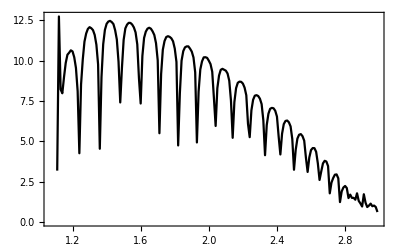

```mathematica
ListPlot[%180,Joined->True,Frame->True,PlotStyle->Black]
```

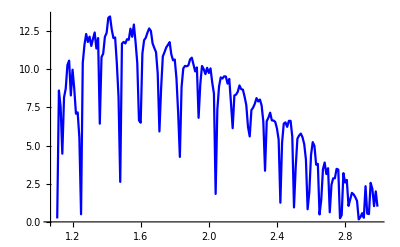

```mathematica
ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,1,25,25,5]},{ω,Range[1.11,2.99,0.01]}],PlotStyle->Blue]
```

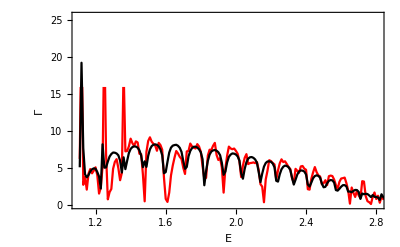

```mathematica
%26
```